# Order of Accuracy Computations

```mathematica
$MinPrecision=2 $MachinePrecision;
```

### Initial pressure, density and velocity profiles

```mathematica
γ = 7/5;
ρL = 4.696; ρR = 1.744;
uL = 0; uR = 311.92;
pL =404400; pR = 101100;
aL = √((γ pL)/ρL); aR = √((γ pR)/ρR);
f[x_]:=Piecewise[{
{(Tanh[√2 Tan[π x/2]] + 1)/2, -1 < x < 1},
{0, x ≤ -1},
{1, x ≥ 1}}];
p[x_ ] = (pR - pL)f[2(x - 6)/2.5 - 1] + pL;
ρ[x_] := Piecewise[{{ρL, x ≤ 6},{ρL/pL^(5/7)p[x]^(5/7), 6 < x < 8.5},{ρR, x ≥ 8.5}}];
u[x_] := Piecewise[{{uL, x ≤ 6},{uR + (2aR)/(γ-1) - 2/(γ-1)√((γ p[x])/ρ[x]), 6 < x < 8.5},{uR, x ≥ 8.5}}];
```

### Initial pressure, density and velocity profiles for x ∈ [6.5, 8]

```mathematica
intermP[x_]:= (pR - pL)(Tanh[√2 Tan[π (2(x - 6)/2.5 - 1)/2]] + 1)/2 + pL;
intermρ [x_]:= ρL/pL^(5/7)intermP[x]^(5/7);
intermU[x_] := uR + (2aR)/(γ-1) - 2/(γ-1)√((γ intermP[x])/intermρ[x]);
sol[x_, t_]:=FindRoot[x == (((2 aL)/(γ - 1))((3 - γ)/4) - ((γ + 1)/4)((2aL)/(γ - 1)(intermP[x0]/pL)^((γ - 1)/(2γ)) - intermU[x0] ))t + x0, {x0, 7.3}];
```

```mathematica
(*intermP[x_]:= (pR + pL)/2 - (pR - pL)/2 Cos[(2π(x-6))/5];
intermρ [x_]:= ρL/pL^(5/7)intermP[x]^(5/7);
intermU[x_] := uR + (2aR)/(γ-1) - 2/(γ-1)√((γ intermP[x])/intermρ[x]);*)
```

### Exact solution for (x, t) ∈ [0, 10]×[0, 0.014] along with plots of the exact solution at t = 0.014

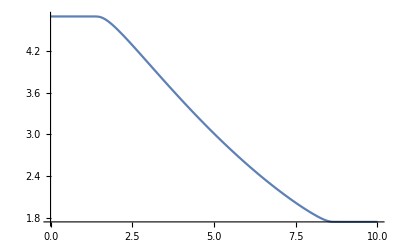

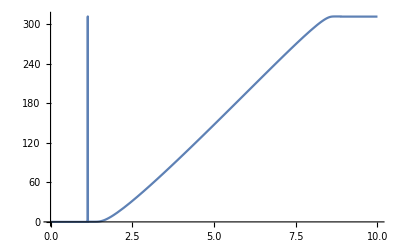

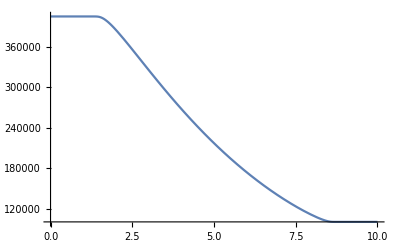

```mathematica
Exactρ[x_, t_] := Piecewise[{
{ρL, x < 6 + t(uL - aL)}, 
{intermρ[x0/.sol[x, t]],  6 + t(uL - aL)≤ x ≤ 8.5 + t(uR - aR) },
{ρR, x > 8.5 + t(uR - aR)}}];
ExactU[x_, t_] := Piecewise[{
{uL, x < 6 + t(uL - aL)}, 
{intermU[x0/.sol[x, t]],  6 + t(uL - aL)≤ x ≤ 8.5 + t(uR - aR) },
{uR, x > 8.5 + t(uR - aR)}}];
ExactP[x_, t_] := Piecewise[{
{pL, x < 6 + t(uL - aL)}, 
{intermP[x0/.sol[x, t]],  6 + t(uL - aL)≤ x ≤ 8.5 + t(uR - aR) },
{pR, x > 8.5 + t(uR - aR)}}];
exactDensity = Plot[Exactρ[x, 0.014], {x, 0, 10}, PlotRange->All]
exactVelocity = Plot[ExactU[x, 0.014], {x, 0, 10}, PlotRange->All]
exactPressure = Plot[ExactP[x, 0.014], {x, 0, 10}, PlotRange->All]
```

### Import data for meshes with 20, 40, 80, 160, 320, 640, and 1280 cells

```mathematica
nodes = 5;
type = "25";
```

```mathematica
data20 = Import["/Users/andrewross/Documents/Euler1D/Euler1D/density_"<>type<>"_(cells=20)_(CFL=0.010000).txt", "Table"];
data40 = Import["/Users/andrewross/Documents/Euler1D/Euler1D/density_"<>type<>"_(cells=40)_(CFL=0.010000).txt", "Table"];
data80 = Import["/Users/andrewross/Documents/Euler1D/Euler1D/density_"<>type<>"_(cells=80)_(CFL=0.010000).txt", "Table"];
data160 = Import["/Users/andrewross/Documents/Euler1D/Euler1D/density_"<>type<>"_(cells=160)_(CFL=0.010000).txt", "Table"];
data320 = Import["/Users/andrewross/Documents/Euler1D/Euler1D/density_"<>type<>"_(cells=320)_(CFL=0.010000).txt", "Table"];
data640 = Import["/Users/andrewross/Documents/Euler1D/Euler1D/density_"<>type<>"_(cells=640)_(CFL=0.010000).txt", "Table"];
data1280 = Import["/Users/andrewross/Documents/Euler1D/Euler1D/density_"<>type<>"_(cells=1280)_(CFL=0.010000).txt", "Table"];
(*ListLogLogPlot[{error20, error40, error80, error160, error320, error640}, Joined->True]*)
```

### Solution points and Quadrature weights

```mathematica
sp=Sort[{x}/.Solve[LegendreP[nodes, x] - LegendreP[nodes-2, x] == 0, x]//Flatten, Less]//Simplify;
W[k_]:=Piecewise[{{2/(nodes(nodes-1)),k == 1 || k == nodes},{2/(nodes(nodes-1))1/LegendreP[nodes-1,sp⟦k⟧]^2, 1 < k < nodes}}];
qw = Table[W[k], {k, 1, nodes}]//Simplify;
```

```mathematica
qw20 = Table[qw((data20⟦nodes, 1⟧ - data20⟦1,1⟧)/2), {i, 1, 20}]//Flatten;
qw40 = Table[qw((data40⟦nodes, 1⟧ - data40⟦1,1⟧)/2), {i, 1, 40}]//Flatten;
qw80 = Table[qw((data80⟦nodes, 1⟧ - data80⟦1,1⟧)/2), {i, 1, 80}]//Flatten;
qw160 = Table[qw((data160⟦nodes, 1⟧ - data160⟦1,1⟧)/2), {i, 1, 160}]//Flatten;
qw320 = Table[qw((data320⟦nodes, 1⟧ - data320⟦1,1⟧)/2), {i, 1, 320}]//Flatten;
qw640 = Table[qw((data640⟦nodes, 1⟧ - data640⟦1,1⟧)/2), {i, 1, 640}]//Flatten;
qw1280 = Table[qw((data1280⟦nodes, 1⟧ - data1280⟦1,1⟧)/2), {i, 1, 1280}]//Flatten;
```

### x-coordinates for computations

```mathematica
Quiet[x20 = Table[x0/.sol[x, 0.014], {x, data20⟦;;, 1⟧}]];
Quiet[x40 = Table[x0/.sol[x, 0.014], {x, data40⟦;;, 1⟧}]];
Quiet[x80 = Table[x0/.sol[x, 0.014], {x, data80⟦;;, 1⟧}]];
Quiet[x160 = Table[x0/.sol[x, 0.014], {x, data160⟦;;, 1⟧}]];
Quiet[x320 = Table[x0/.sol[x, 0.014], {x, data320⟦;;, 1⟧}]];
Quiet[x640 = Table[x0/.sol[x, 0.014], {x, data640⟦;;, 1⟧}]];
Quiet[x1280 = Table[x0/.sol[x, 0.014], {x, data1280⟦;;, 1⟧}]];
```

### List plots of the numerical solution on grids with 20, 40, 80, 160, 320, 640, and 1280 cells

```mathematica
Quiet[lp20 = ListPlot[Transpose[{data20⟦;;, 1⟧, ρ/@x20}], PlotMarkers -> {Automatic, 4.5}];
lp40 = ListPlot[Transpose[{data40⟦;;, 1⟧, ρ/@x40}], PlotMarkers -> {Automatic, 4.5}];
lp80 = ListPlot[Transpose[{data80⟦;;, 1⟧, ρ/@x80}], PlotMarkers -> {Automatic, 4.5}];
lp160 = ListPlot[Transpose[{data160⟦;;, 1⟧, ρ/@x160}], PlotMarkers -> {Automatic, 4.5}];
lp320 = ListPlot[Transpose[{data320⟦;;, 1⟧, ρ/@x320}], PlotMarkers -> {Automatic, 4.5}];
lp640 = ListPlot[Transpose[{data640⟦;;, 1⟧, ρ/@x640}], PlotMarkers -> {Automatic, 4.5}];
lp1280 = ListPlot[Transpose[{data1280⟦;;, 1⟧, ρ/@x1280}], PlotMarkers -> {Automatic, 4.5}];]
```

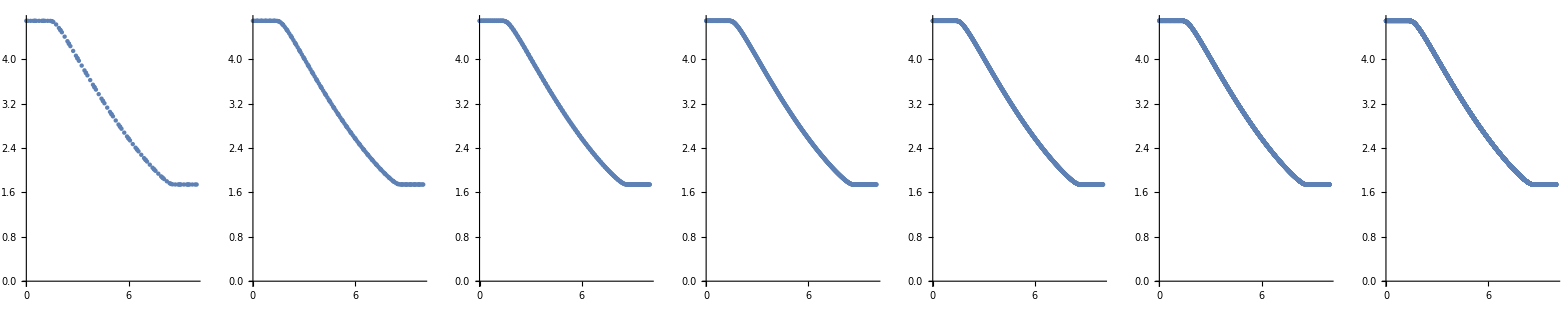

```mathematica
GraphicsGrid[{{lp20, lp40, lp80, lp160, lp320, lp640, lp1280}}]
```

### error computations

```mathematica
Error[x_, d_, qw_]:= √((Plus@@((ρ/@x - d⟦;;, 2⟧)^2 qw))/10);
```

```mathematica
e20 = Error[x20, data20, qw20];
e40 = Error[x40, data40, qw40];
e80 = Error[x80, data80, qw80];
e160 = Error[x160, data160, qw160];
e320 = Error[x320, data320, qw320];
e640 = Error[x640, data640, qw640];
e1280 = Error[x1280, data1280, qw1280];
```

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

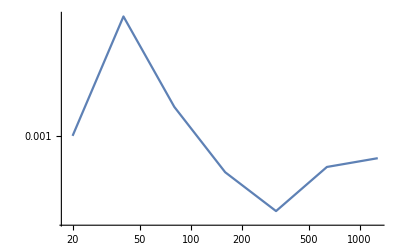

```mathematica
ListLogLogPlot[Transpose[{{20, 40, 80, 160, 320, 640, 1280},{e20, e40, e80, e160, e320, e640, e1280}}], Joined -> True ]
```

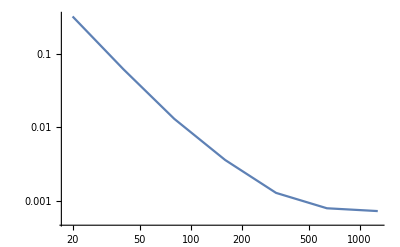
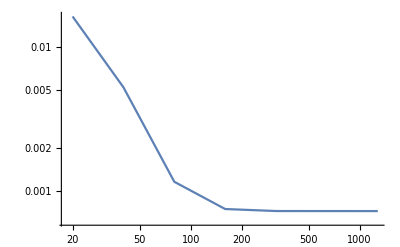
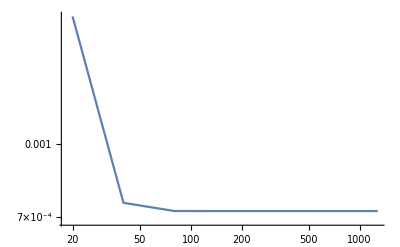
```mathematica
Show[-Graphics-, -Graphics-, -Graphics-, -Graphics-]
```

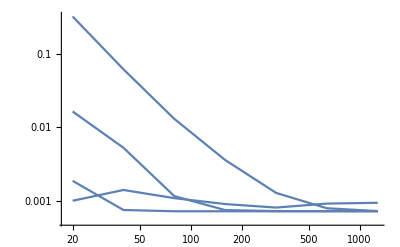

```mathematica
{Log[e20/e40]/Log[2],Log[e40/e80]/Log[2],Log[e80/e160]/Log[2],Log[e160/e320]/Log[2],Log[e320/e640]/Log[2],Log[e640/e1280]/Log[2]}
```

{-0.487462,0.369205,0.266736,0.158604,-0.180124,-0.0358155}

## Error plots

### Log-Log plots of the entropy errors along with computations of the respective convergence rates

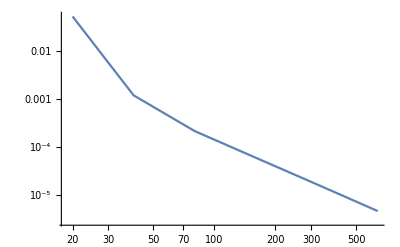

```mathematica
(*  type: 22  *)
```

```mathematica
((*  type: 22  *)
Log[error20⟦2⟧/error40⟦2⟧])/Log[2]
Log[error40⟦2⟧/error80⟦2⟧]/Log[2]
Log[error80⟦2⟧/error160⟦2⟧]/Log[2]
Log[error160⟦2⟧/error320⟦2⟧]/Log[2]
Log[error320⟦2⟧/error640⟦2⟧]/Log[2]
```

5.46257

2.47447

1.8448

1.84015

1.85608

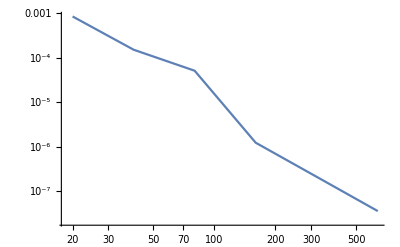

```mathematica
(*  type: 23  *)
```

```mathematica
((*  type: 23  *)
Log[error20⟦2⟧/error40⟦2⟧])/Log[2]
Log[error40⟦2⟧/error80⟦2⟧]/Log[2]
Log[error80⟦2⟧/error160⟦2⟧]/Log[2]
Log[error160⟦2⟧/error320⟦2⟧]/Log[2]
Log[error320⟦2⟧/error640⟦2⟧]/Log[2]
```

2.48393

1.56915

5.37565

2.54945

2.55628

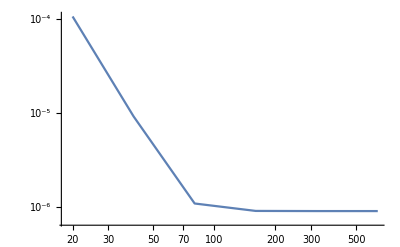

```mathematica
(*  type: 24  *)
```

```mathematica
((*  type: 24  *)
Log[error20⟦2⟧/error40⟦2⟧])/Log[2]
Log[error40⟦2⟧/error80⟦2⟧]/Log[2]
Log[error80⟦2⟧/error160⟦2⟧]/Log[2]
Log[error160⟦2⟧/error320⟦2⟧]/Log[2]
Log[error320⟦2⟧/error640⟦2⟧]/Log[2]
```

3.53864

3.0795

0.262927

0.005137

0.000338603

## HOFV Interpolation Formulas

```mathematica
(*  ASIDE: table indexing ...  *)
NumberOfRows = 3; NumberOfColumns = 5;
Table[0, {i, 1, NumberOfRows}, {j, 1, NumberOfColumns}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

### Least squares to find interpolated values at left/right cell boundaries

```mathematica
distance = 1;  (*  number of neighbouring cells to visit | order = 1, 2 ⟹ distance = 1 | order = 3, 4 ⟹ distance = 2  *)
order = 1;        (*  order of solution reconstruction  *)
DD = Table[(i Δx)^j/(j!), {i, -distance, distance}, {j, 1, order}];
Y = Table[(U[i] - U[0]), {i,-distance, distance}, {j, 1, 1} ];
DTD = Transpose[DD].DD//Simplify;
DTY = Transpose[DD].Y//Simplify;
X = LinearSolve[DTD, DTY];
u[x_]:= U[0] + Sum[X⟦i, 1⟧(x^i/(i!)), {i, 1, order}];

(*  ----- OUTPUT -----  *)
 Det[DTD]
 DTD//MatrixForm
 DTY //MatrixForm
 X//MatrixForm
u[Δx/2]//Simplify       (*  right cell boundary  *)
u[-Δx/2]//Simplify    (*  left cell boundary  *)
```

2 Δx^2

(2 Δx^2)

(Δx (-U[-1]+U[1]))

((-U[-1]+U[1])/(2 Δx))

U[0]+1/4 (-U[-1]+U[1])

U[0]+1/4 (U[-1]-U[1])